```mathematica
(*Контрольная работа 1*)
(*Задача 1*)
```

```mathematica
A={{1/2, 1/3, 1/2, 1}, {1/3, 1/2, 1, 1/2}, {1/2, 1, 1/2,1/3}, {1, 1/2, 1/3, 1/2}} 
Det[A]
MatrixForm[RowReduce[A]]
Eigenvectors[A]
```

{{1/2,1/3,1/2,1},{1/3,1/2,1,1/2},{1/2,1,1/2,1/3},{1,1/2,1/3,1/2}}

28/81

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

{{1,1,1,1},{-1,-1,1,1},{1,-1,-1,1},{-1,1,-1,1}}

```mathematica
(*Задача 2*)
Integrate[(Cos[x])^5 √Sin[x], x]
Clear[x]
```

2/231 Sin[x]^(3/2) (77-66 Sin[x]^2+21 Sin[x]^4)

```mathematica
(*Задача 3*)
h[x_] := x Sinh[x]
g[x_]:= D[h[y], {y, 100}]/.y->x
g[x] //Simplify
g[0] 
Clear[h, g, x]
```

100 Cosh[x]+x Sinh[x]

100

{{y[x]→-(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))},{y[x]→(√2)/(√(1+2 x+2 ⅇ^(2 x) C[1]))}}

-(√2)/(√(1+2 ⅇ^(2 x)+2 x))

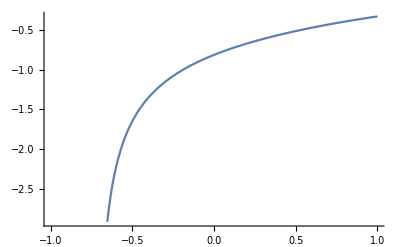

```mathematica
(*Задача 4*)
res = DSolve[y'[x]+y[x]== x*y[x]^3, y[x], x]

f[x_] = y[x]/.res⟦1⟧/.{C[1]-> 1}
Plot[f[x],{x, -1, 1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

{InterpolatingFunction[…][x]}

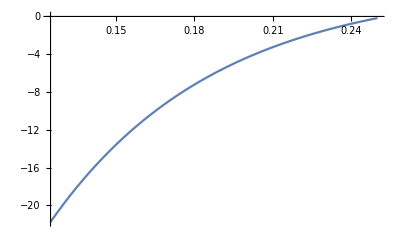

```mathematica
(*Задача 5*)
Clear[y,x,t];
ress = NDSolve[{y''[x]+16y'[x] +2y[x] == 16/Sin[4x], y[π/8] ==3,y'[π/8]==2π},y[x],{x,1/8,1/4}]
t[x_] = y[x]/.ress

Plot[t[x], {x, 1/8,1/4}]
```

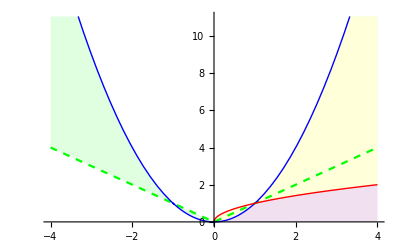

```mathematica
(*Контрольная работа 2*)
(*Задача 1*)
Plot[{Abs[x],x^2,√x}, {x, -4, 4}, PlotStyle->{{Green, Dashed}, {Blue, Thin},{Red, Thick}},Filling->{{1->{{2}, LightGreen}}, {2-> {{3}, LightYellow}},{3-> {Axis, LightPurple}}}]
```

```mathematica
(*Задача 2*)
Clear[r,ϕ];
r[ϕ_]:=10*Cos[ϕ]/(Sin[ϕ])^2;
PolarPlot[r[ϕ],{ϕ,-π,π},ColorFunction->Function[{x,y,ϕ},Hue[Abs[r[ϕ]/1000]]],ColorFunctionScaling->False]
```

-Graphics-

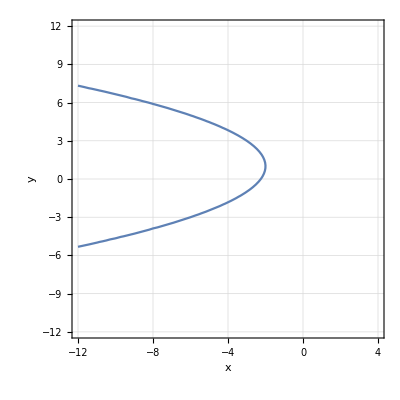

```mathematica
(*Задача 3*)
ContourPlot[y^2-2y+4x+9==0,{x,-12,4},{y,-12,12}, Axes->True, GridLines->Automatic, AxesLabel-> {x,y}]
```

```mathematica
(*Задача 4*)
ClearAll;
 Manipulate[b=(a⟦1⟧+a⟦2⟧)/2;c=(a⟦2⟧+a⟦3⟧)/2;
d=(a⟦3⟧+a⟦4⟧)/2;e=(a⟦4⟧+a⟦1⟧)/2;
Column[{Graphics[GraphicsComplex[a~Join~{(a⟦1⟧+a⟦2⟧)/2,(a⟦2⟧+a⟦3⟧)/2,(a⟦3⟧+a⟦4⟧)/2,(a⟦4⟧+a⟦1⟧)/2},{Line[{1,2,3,4,1}],Orange,Thick,Line[{5,6,7,8,5}],Red,PointSize[Medium],Point[{1,2,3,4}],Black,PointSize[Medium],Point[{5,6,7,8}]}]],Row[{"Коллинеарны 1 и 3 стороны:",If[(((b-c)⟦1⟧)/((e-d)⟦1⟧)-((b-c)⟦2⟧)/((e-d)⟦2⟧))<0.0001,Row[{"Да и коэффициент = ",((b-c)⟦1⟧)/((e-d)⟦1⟧)}],"Нет"]}],Row[{"Коллинеарны 2 и 4 стороны:",If[(((b-e)⟦1⟧)/((c-d)⟦1⟧)-((b-e)⟦2⟧)/((c-d)⟦2⟧))<0.0001,Row[{"Да и коэффициент = ",((b-e)⟦1⟧)/((c-d)⟦1⟧)}],"Нет"]}]}],{{a,{{0,0},{1,0},{1,1},{0,1}}},Locator}]
```

```mathematica
(*Задача 5*)
Manipulate[Graphics3D[{Brown, Cuboid[{0,0,0}], Blue, Arrow[{{0,0,0},{a1,a2,a3}}],Red, Arrow[{{0,0,0},{b1,b2,b3}}], Green,Arrow[{{0,0,0},{-a1-b1,-a2-b2,-a3-b3}}]}], {a1, -12,12},{a2, -12,12},{a3, -12,12},{b1, -12,12},{b2, -12,12},{b3, -12,12}]
```

```mathematica
(*Задача 6*)
ClearAll;
ell[u_, v_]:={2Sin[u]Cos[v], 4Sin[u]Sin[v], 5Cos[u]};
iForm[r_][u_,v_]:=Module[{ru, rv}, ru=D[r[u,v],u];rv=D[r[u,v],v];
({{ru.ru, ru.rv}, {ru.rv, rv.rv}})];
norm[r_][u_, v_]:=Module[{ru, rv, nn}, ru=D[r[u,v],u];rv=D[r[u,v],v];nn=Cross[ru,rv];
nn/(√(nn.nn))];
iiForm[r_][u_,v_]:=Module[{ruu,ruv,rvv,n},
n=norm[r][u,v];
ruu=D[r[u,v],u,u];
ruv=D[r[u,v],u,v];
rvv=D[r[u,v],v,v];
({{ruu.n, ruv.n}, {ruv.n, rvv.n}})];
k[r_][u_,v_]:=Det[iiForm[r][u,v]]/Det[iForm[r][u,v]];

g[u_, v_]=k[ell][u,v] // Simplify;
kMax=Maximize[g[u,v], {u,v}]⟦1⟧;
kMin=Minimize[g[u,v], {u,v}]⟦1⟧;
kRescaled[u_,v_]:=(g[u,v]-kMin)/(1.1(kMax-kMin));
ParametricPlot3D[{2Sin[u]Cos[v], 4Sin[u]Sin[v], 5Cos[u]},{u,0,2π},{v,-π,π},ColorFunction->Function[{x,y,z, u, v},Hue[kRescaled[u,v]]],ColorFunctionScaling->False]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

-Graphics3D-

```mathematica
(*Зачетная задача*)
Clear[t,ϕ,h];
f[a_,b_,ϕ_]:={a Cos[ϕ],b Sin[ϕ]}
sol[a_,b_,c_,d_]:=NSolve[{u^2/a^2+v^2/b^2-1==0,(c*u)/a^2+(d*v)/b^2-1==0},{u,v}]
soll1[a_,b_,c_,d_]:=u/.sol[a,b,c,d]⟦1,1⟧;
soll2[a_,b_,c_,d_]:=v/.sol[a,b,c,d]⟦1,2⟧;
soll3[a_,b_,c_,d_]:=u/.sol[a,b,c,d]⟦2,1⟧;
soll4[a_,b_,c_,d_]:=v/.sol[a,b,c,d]⟦2,2⟧;
t={};
bil1[a_,b_,c_,d_,n_]:=(t = {};AppendTo[t,{a,b}];AppendTo[t,{soll1[c,d,a,b],soll2[c,d,a,b]}];
AppendTo[t,{2*soll1[c,d,a,b]-a,2*soll2[c,d,a,b]-b}];
For[j=1,j<n - 1,j++,AppendTo[t,{t⟦3j,1⟧,t⟦3j,2⟧}];

If[((soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,1⟧)&&(soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,2⟧)),AppendTo[t,{soll1[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧],soll2[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]}],AppendTo[t,{soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧],soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]}]];If[((soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,1⟧)&&(soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,2⟧)),AppendTo[t,{2*soll1[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,1⟧,2*soll2[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,2⟧}],AppendTo[t,{2*soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,1⟧,2*soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,2⟧}]]];
t);
bil2[a_,b_,c_,d_,n_]:=( t = {};AppendTo[t,{a,b}];AppendTo[t,{soll3[c,d,a,b],soll4[c,d,a,b]}];
AppendTo[t,{2*soll3[c,d,a,b]-a,2*soll4[c,d,a,b]-b}];
For[j=1,j<n - 1,j++,AppendTo[t,{t⟦3j,1⟧,t⟦3j,2⟧}];

If[((soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,1⟧)&&(soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,2⟧)),AppendTo[t,{soll1[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧],soll2[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]}],AppendTo[t,{soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧],soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]}]];If[((soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,1⟧)&&(soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]==t⟦3j-1,2⟧)),AppendTo[t,{2*soll1[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,1⟧,2*soll2[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,2⟧}],AppendTo[t,{2*soll3[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,1⟧,2*soll4[c,d,t⟦3j+1,1⟧,t⟦3j+1,2⟧]-t⟦3j+1,2⟧}]]];
t);

p[a_,b_,c_,d_,n_,k_]:=(Switch[k,"first",h=1,"second",h=2];If[ h == 1,Line[bil1[a,b,c,d,n]],Line[bil2[a,b,c,d,n]]]);
Manipulate[Show[ParametricPlot[f[a,b,ϕ],{ϕ,0,2π},PlotRange->{{-5,5},{-5,5}},ImageSize->{580,580}],Graphics[Point[{z⟦1⟧,z⟦2⟧}];p[z⟦1⟧,z⟦2⟧,a,b,n,k] ]],{a,1,16},{b,1,16},{{z,{a,b}},Locator},{n,2,16},{k,{"first","second"},ControlType->SetterBar}]
```